```mathematica
imgurLogo=-Graphics-;
```

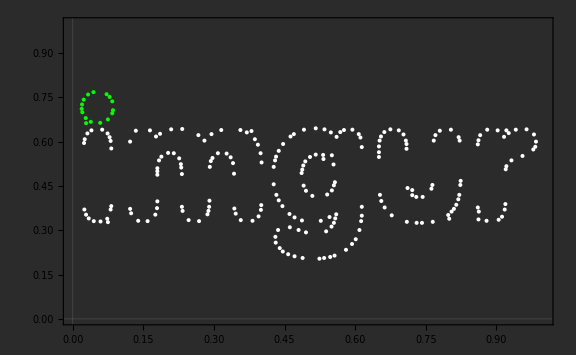

```mathematica
ic=ImageCorners[CornerFilter[imgurLogo]];
ic[[All,1]]/=1400;
ic[[All,1]]+=0.015;
ic[[All,2]]/=1400/GoldenRatio;
ic[[All,2]]+=0.2;
outic=Reap[ (*I really wasnt able to vectorize this...*)
For[i=1,i≤Length[ic],++i,
getme=1;
For[j=i+1,j≤Length[ic],++j,
If[Norm[ic[[i]]-ic[[j]]]<0.01,getme=0;Break;];
]
If[getme==1,Sow[ic[[i]]]];
]
];
gravPoints=outic[[2,1,All]];
fic=Select[gravPoints,#[[2]]<0.65&];
fic2=Select[gravPoints,#[[2]]≥0.65&];
gravImg=Show[ListPlot[fic,PlotTheme->"Scientific",PlotRange->{{0,1},{0,1}},Background->RGBColor[43/255,43/255,43/255],PlotStyle->{White,PointSize[0.005]},ImageSize->Large,FrameStyle->White],ListPlot[fic2,PlotStyle->{Green,PointSize[0.005]}]]
```

```mathematica
tmax=0.5;
n=Length[gravPoints];
sol=ParametricNDSolve[{{x''[t],y''[t]}==Sum[ζ/(Norm[gravPoints[[k]]-{x[t],y[t]}]^2)*Normalize[gravPoints[[k]]-{x[t],y[t]}],{k,1,n}],{x[0],y[0]}=={0.9,0.95},{x'[0],y'[0]}=={-3,0}},{x[t],y[t]},{t,0,tmax},{ζ}];
xp=(x[t]/.sol);
yp=(y[t]/.sol);
```

```mathematica
Monitor[
imgs=Table[Show[gravImg,Table[ParametricPlot[{xp[ζ]/.t->T,yp[ζ]/.t->T},{T,0,ct},PlotStyle->{Opacity[0.1,White],Thickness[0.0001]}],{ζ,0.03,0.1,0.001}]],{ct,tmax/100,tmax,tmax/100}];,ct]
```

```mathematica
Export[NotebookDirectory[]<>"ImgurParametricGravitationalGrid.gif",imgs]
```

C:\Users\Julien\Desktop\Science Animations\ImgurParametricGravitationalGrid\ImgurParametricGravitationalGrid.gif